```mathematica
<<"C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

Location of XPS excel file.

```mathematica
XPSPath="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

## Fitting Example Data

### Example 1: Sample carbon 1s edge

First, generate some fake data from example peak positions for a carbon 1s edge:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

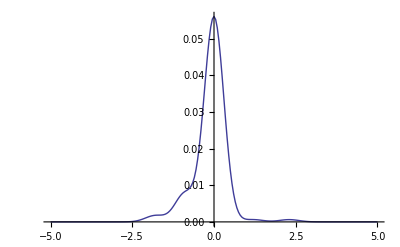

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals: 1.1726286654736552e-6

Weights | Means | σs
0.835823 | -0.000301534 | -0.298856
0.0230805 | 1.57939 | 0.930734
0.000121753 | -6.38624 | -0.0542647
0.115619 | -0.897707 | 0.303996
0.0253557 | -1.80639 | 0.295499

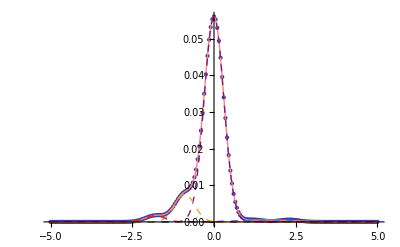

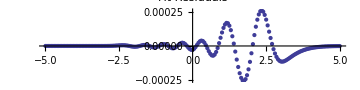

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Perfect results can be obtained by lowering the scaling factor.

Sum of squares of residuals: 1.4818850581755128e-15

Weights | Means | σs
0.11419 | -0.9 | 0.3
0.00932165 | 2.3 | -0.300003
0.0258933 | -1.8 | -0.299999
0.00932163 | 1.19999 | -0.300002
0.841274 | -2.74128×10^-8 | -0.3

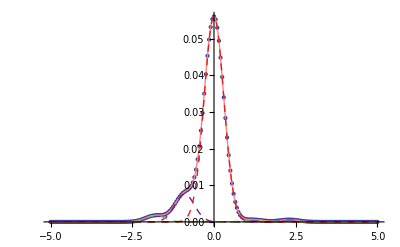

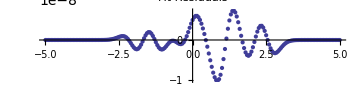

```mathematica
ExCModel=Model[ExampleCData,5,0.75];
FitSummary[ExampleCData,ExCModel];
```

### Example 2: Sample carbon 1s edge with broader peaks

Broaden the peaks from example 1. The data appears to be much harder to fit!

0.0036 ⅇ^(-3.125 (-2.3+x)^2)+0.0036 ⅇ^(-3.125 (-1.2+x)^2)+0.3249 ⅇ^(-3.125 x^2)+0.0441 ⅇ^(-3.125 (0.9+x)^2)+0.01 ⅇ^(-3.125 (1.8+x)^2)

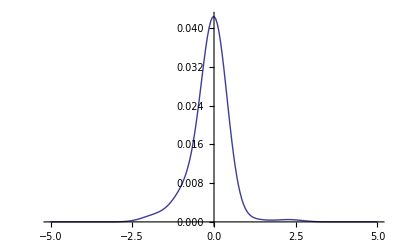

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.4,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Try to fit this data with default values. It does a pretty good job, but misses the distinction between the peak at 1.2 and 2.3 eV.

Sum of squares of residuals: 1.8697928718519927e-6

Weights | Means | σs
0.0138971 | -0.604531 | 0.645208
0.00346139 | 0.0789347 | 1.70922
0.937578 | -6.87649 | -0.325552
0.0450636 | 0.0163255 | 0.38633
7.15168×10^-16 | 1.44734 | 4.14948

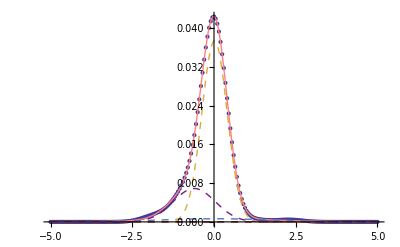

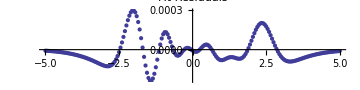

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Here, decreasing the scaling factor again produces a better fit that exactly reproduces the data.

Sum of squares of residuals: 1.1977412153901936e-11

Weights | Means | σs
0.114599 | -0.899507 | -0.400826
0.00945934 | 1.19946 | 0.40517
0.0257598 | -1.80187 | -0.399279
0.840926 | 0.000092014 | 0.3999
0.00925555 | 2.30306 | 0.398036

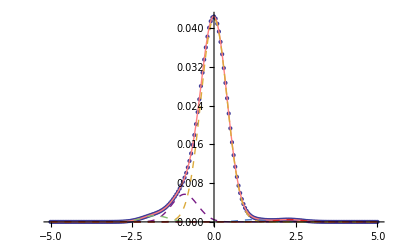

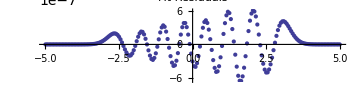

```mathematica
ExCModel=Model[ExampleCData,5,0.65];
FitSummary[ExampleCData,ExCModel];
```

### Example 3: Sample carbon 1s edge with narrower peaks

Make the peaks in example 1 more narrow.

0.0036 ⅇ^(-12.5 (-2.3+x)^2)+0.0036 ⅇ^(-12.5 (-1.2+x)^2)+0.3249 ⅇ^(-12.5 x^2)+0.0441 ⅇ^(-12.5 (0.9+x)^2)+0.01 ⅇ^(-12.5 (1.8+x)^2)

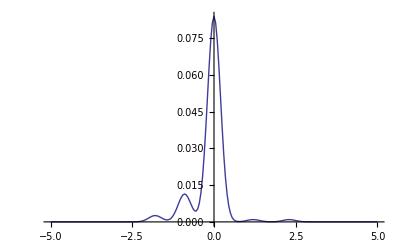

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.2,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Again, the default values do an OK job, but miss the higher energy peaks:

Sum of squares of residuals: 4.756865249060735e-6

Weights | Means | σs
0.114094 | -0.899957 | 0.200167
0.0211987 | 1.69745 | 0.829156
3.82969×10^-8 | -6.69536 | 1.72406
0.838852 | -0.000210575 | 0.199695
0.0258551 | -1.80009 | 0.199857

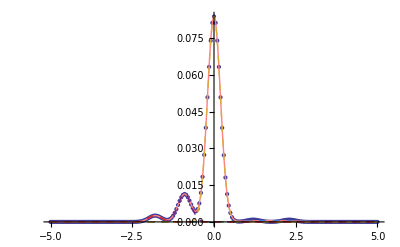

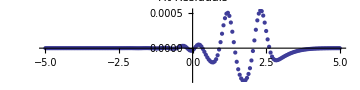

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Again, decreasing the scaling factor slightly gets precisely the correct result. Althoug it seems as if the choice of scaling factor should be more robust in this case, it does not appear to be.

Sum of squares of residuals: 1.4952663458090157e-15

Weights | Means | σs
0.0093216 | 1.2 | 0.200001
0.841274 | -8.13229×10^-9 | -0.2
0.0258933 | -1.8 | -0.2
0.00932164 | 2.3 | 0.200002
0.11419 | -0.9 | 0.2

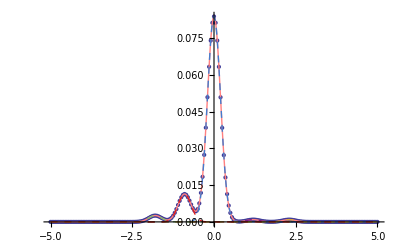

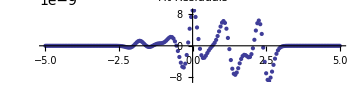

```mathematica
ExCModel=Model[ExampleCData,5,0.65];
FitSummary[ExampleCData,ExCModel];
```

### Example 4: Sample carbon 1s edge plus noise

Generate the same data, but add some noise:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

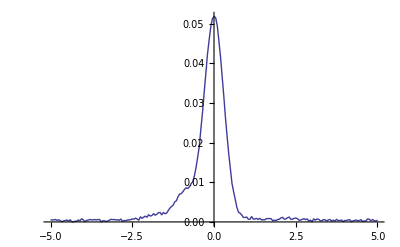

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Fitting this data is more difficult. We can again reproduce the qualitative features fairly well. However, the higher energy peaks are lost and the lower energy peaks are mixed together.

Sum of squares of residuals: 0.0000152001202735005

Weights | Means | σs
0.133052 | -0.172362 | 0.215395
0.144108 | -0.13273 | -3.07736
0.00110256 | 2.72934 | -0.00932663
0.536666 | 0.0758175 | -0.269638
0.185071 | -0.662982 | -0.49634

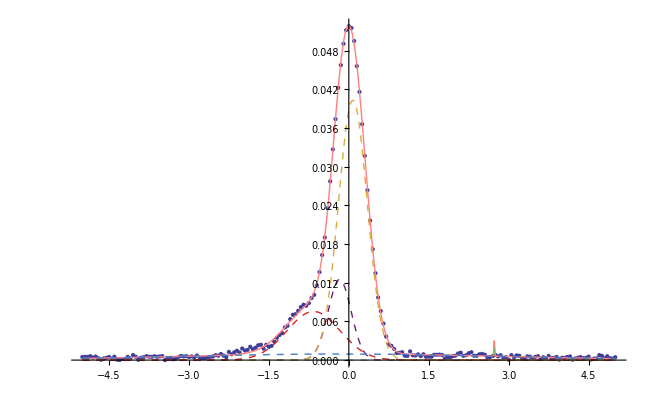

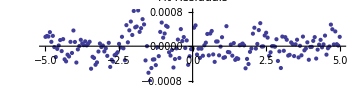

```mathematica
ExCModel=Model[ExampleCData,5];
FitSummary[ExampleCData,ExCModel];
```

Using the same parameters that were “good” before now yield obviously bad results.

Sum of squares of residuals: 0.00041828530526664054

Weights | Means | σs
0.00202778 | -0.015278 | 0.319531
0.163593 | -150.436 | 60.9238
3.60125×10^-15 | 40.2661 | -10.1299
0.138045 | -31.2364 | -0.0798249
0.696335 | 43.006 | 2.00101

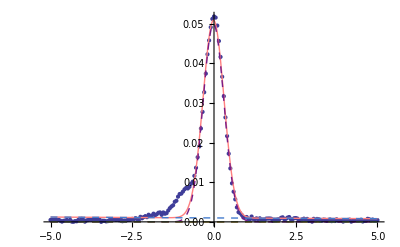

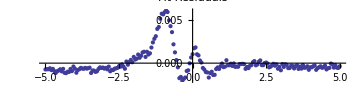

```mathematica
ExCModel=Model[ExampleCData,5,0.75];
FitSummary[ExampleCData,ExCModel];
```

Increasing the scaling factor slightly more does a good job of fitting the lower energy peaks, though the higher energy peaks are again lost.

Sum of squares of residuals: 9.264718679109545e-6

Weights | Means | σs
3.06036×10^-15 | -1.29625 | -1.11865
0.134998 | 0.238204 | -3.58036
0.0165686 | -1.79353 | -0.278683
0.747346 | 0.000203472 | -0.297975
0.101087 | -0.89592 | 0.302715

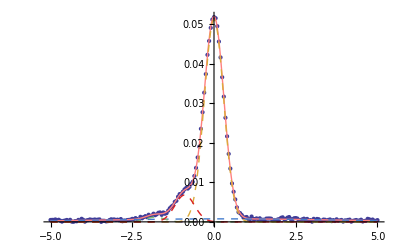

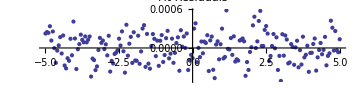

```mathematica
ExCModel=Model[ExampleCData,5,0.8];
FitSummary[ExampleCData,ExCModel];
```

Increasing the amount of noise makes fitting even more challenging. Try it!

### Example 5: Sample carbon 1s edge plus noise, using known peak locations

We saw before that fitting with noise was a bit challenging. Let’s look at that data again:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

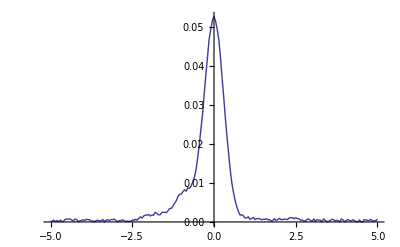

```mathematica
exweights={.10,.21,.57,.06,.06}^2; (*A^2 values, then plug in A values below*)
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[Sqrt[exweights[[i]]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0.005*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

Instead of fitting the data with completely free parameters, we can use known (or suspected) positions of the peaks using the FixedPeaksModel command. The default parameters do an abysmal job:

Sum of squares of residuals: 0.025698740956404963

Weights | σs
0.000623727 | -88.1705
7.50429×10^-6 | 310.62
0.143655 | 35.2693
0.108391 | -86.4953
0.747323 | 46.9712

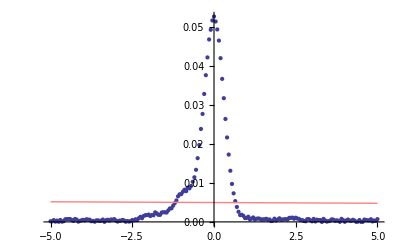

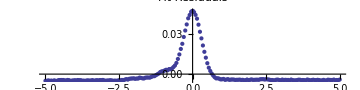

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions];
FitSummary[ExampleCData,ExCModel,True];
```

Again, reducing the scaling factor makes all the difference, although the high-energy peaks are still lost in the noise.

Sum of squares of residuals: 0.000011950788835789684

Weights | σs
0.0232344 | -0.318772
0.0958686 | 0.299067
0.711192 | 0.299226
0.159999 | 7.88326
0.00970575 | -0.779551

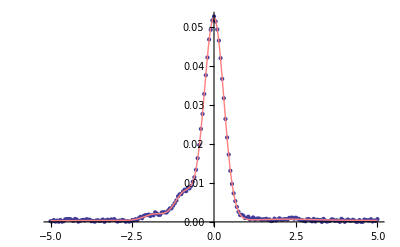

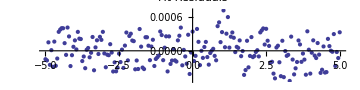

```mathematica
ExCModel=FixedPeaksModel[ExampleCData,expositions,0.6];
FitSummary[ExampleCData,ExCModel,True];
```

This result is somewhat robust against perturbations in the peak positions (in case we guess wrong). Here we change the peak positions by a random amount up to 10%. (Pushing this up to 20% makes the fit obviously bad in some cases.)

Sum of squares of residuals: 0.00001809572013365

Weights | σs
0.0236753 | -0.349599
0.0842876 | 0.264578
0.743538 | 0.304092
0.145925 | -5.53448
0.00257436 | -0.12513

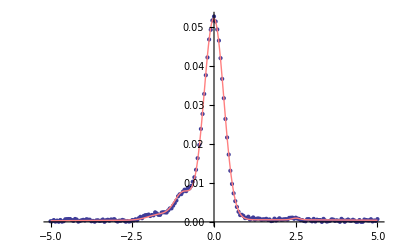

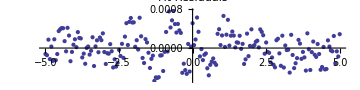

Sum of squares of residuals: 0.0000207704910576396

Weights | σs
0.0156437 | -0.23049
0.0926839 | -0.30962
0.697954 | 0.303722
0.00460014 | -0.248911
0.189119 | 9.05805

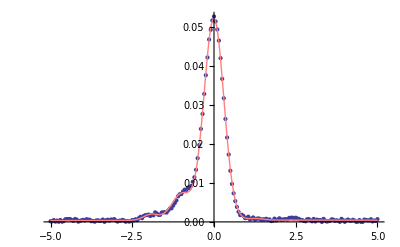

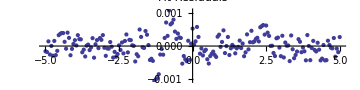

Sum of squares of residuals: 0.000025237790215703825

Weights | σs
0.0158875 | -0.235014
0.0889756 | 0.279179
0.74345 | -0.304858
0.151686 | -5.4081
1.67626×10^-14 | 2.61954

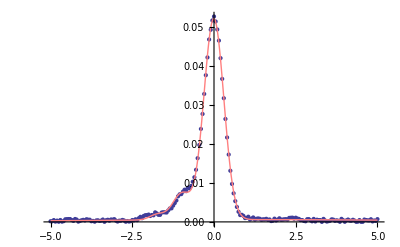

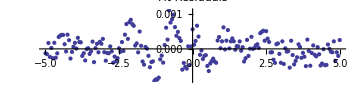

Sum of squares of residuals: 0.000012994899340660118

Weights | σs
0.0141886 | -0.274407
0.0657202 | -0.297178
0.49383 | -0.301855
0.416935 | -35.358
0.00932535 | 0.807403

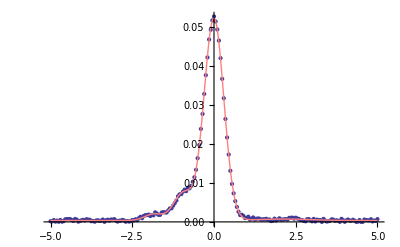

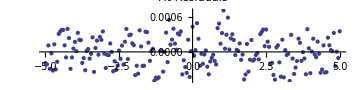

Sum of squares of residuals: 0.00001172548647282835

Weights | σs
0.00251679 | 0.265074
0.0155274 | -0.353897
0.0964383 | 0.29414
0.00350311 | 1.26428
0.882014 | 385.286

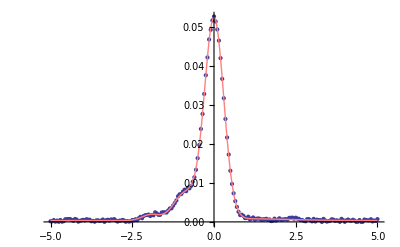

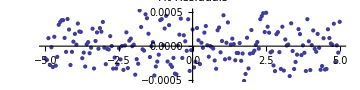

{Null,Null,Null,Null,Null}

```mathematica
Table[
ExCModel=FixedPeaksModel[ExampleCData,(#*RandomReal[{0.9,1.1}])&/@expositions,0.6];
FitSummary[ExampleCData,ExCModel,True];
,{i,1,5}
]
```

## Bulk fitting of actual XPS data

### Carbon Peak

#### Setup

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,8];
```

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

#### Fitting with free parameters

```mathematica
AllCModels=Model[#,5]&/@CenteredCData;
```

Sum of squares of residuals: 2.634072808276322e-6

Weights | Means | σs
0.187847 | -0.26884 | -0.631945
0.136843 | 0.844375 | 1.13513
0.00906364 | 3.75123 | 0.659571
0.501577 | 0.0539486 | -0.39266
0.164669 | 0.0268209 | 0.269554

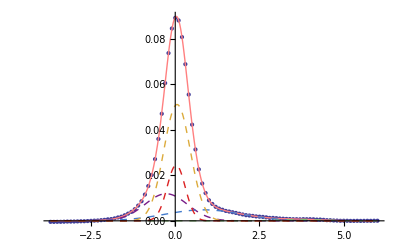

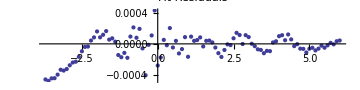

Sum of squares of residuals: 0.00004828053288786465

Weights | Means | σs
7.08273×10^-14 | -0.0989099 | 0.600606
2.09667×10^-15 | -5.44581 | -0.813362
0.415501 | -0.171064 | 1.39235
6.03823×10^-16 | 0.283696 | -1.14305
0.584499 | -0.00545863 | 0.344538

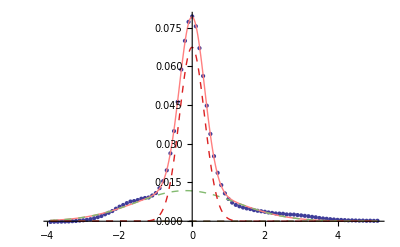

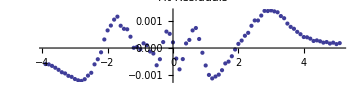

Sum of squares of residuals: 8.493731300076574e-7

Weights | Means | σs
0.321741 | -0.160565 | -0.916303
2.86922×10^-11 | -0.623896 | 1.55987
0.0431167 | 2.40203 | 0.794958
0.0365139 | -0.020738 | -0.190989
0.598628 | 0.0300335 | -0.328362

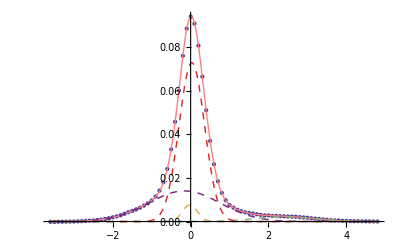

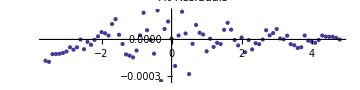

Sum of squares of residuals: 8.931706356661189e-6

Weights | Means | σs
0.0701353 | -0.201969 | 0.781938
0.696712 | -8.85647 | 0.172399
0.041028 | 0.816304 | 1.58034
0.192125 | -0.00966036 | 0.320652
2.77461×10^-13 | 0.914509 | -3.51288

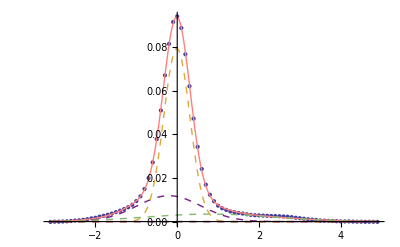

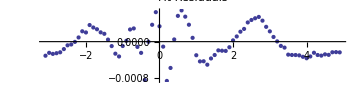

Sum of squares of residuals: 3.34058708440817e-6

Weights | Means | σs
0.122368 | 0.854498 | -1.45083
0.343886 | -0.138276 | 0.610766
2.78388×10^-12 | -1.22283 | -0.961273
0.458697 | -0.0160865 | 0.320426
0.0750492 | 17.2204 | 7.48165

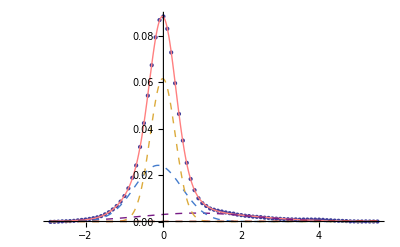

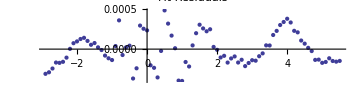

Sum of squares of residuals: 5.878196116188044e-7

Weights | Means | σs
0.321477 | -0.31866 | -0.760631
0.0451224 | 1.46273 | -0.695333
0.358302 | 0.0553012 | 0.396756
0.261474 | 0.0527528 | -0.27405
0.0136236 | 2.97256 | 0.679798

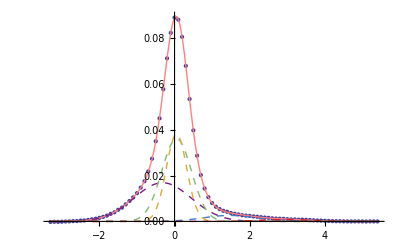

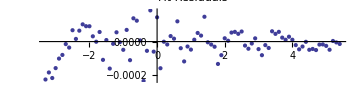

Sum of squares of residuals: 3.8585654896187324e-6

Weights | Means | σs
0.485265 | 0.0238017 | -0.32855
0.026707 | 2.51796 | -0.618142
0.205105 | 7.5911 | 0.208651
1.87068×10^-15 | -4.7235 | -10.7612
0.282924 | -0.146538 | 0.96791

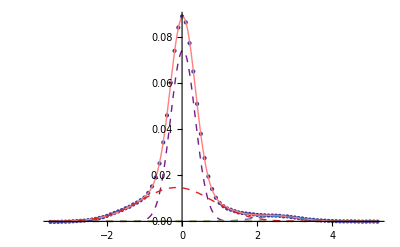

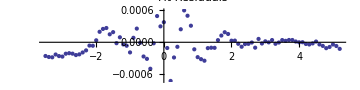

Sum of squares of residuals: 3.723540755191463e-6

Weights | Means | σs
0.55132 | 0.0489455 | -0.321548
0.293045 | -0.0775562 | 0.943119
0.123202 | 10.9018 | -0.0116027
0.0324334 | 2.5198 | -0.660621
5.6412×10^-13 | -3.43041 | -3.28095

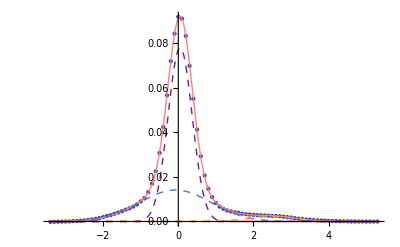

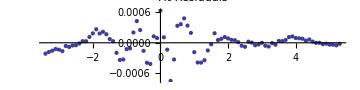

Sum of squares of residuals: 4.904982407228656e-6

Weights | Means | σs
1.15479×10^-14 | 5.6955 | -7.97886
1.41965×10^-14 | -19.0162 | -5.3385
0.347272 | -0.167889 | -0.972239
0.621829 | -0.0320048 | -0.330791
0.0308998 | 2.49143 | 0.584304

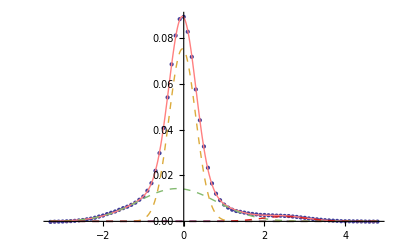

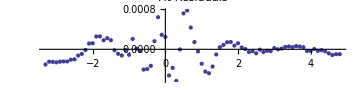

Sum of squares of residuals: 8.878473388643823e-7

Weights | Means | σs
0.10462 | -0.946514 | 0.668093
0.404386 | 0.0399072 | -0.288991
0.0225036 | 1.33964 | 0.362217
0.0474223 | 2.30253 | 0.734165
0.421068 | 0.0924282 | 0.477623

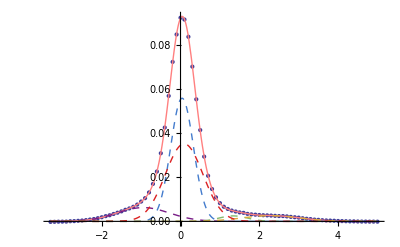

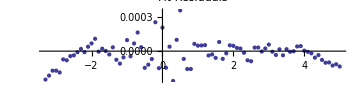

Sum of squares of residuals: 5.0413534301028505e-6

Weights | Means | σs
5.66957×10^-14 | -0.636565 | -2.35656
0.0141574 | 2.76115 | 0.588425
0.346272 | -0.170528 | -1.27708
0.633313 | 0.0334005 | -0.358047
0.00625792 | -0.710362 | -0.170054

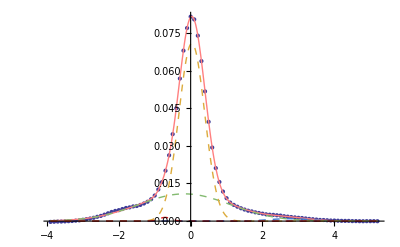

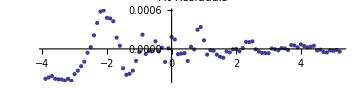

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length[CenteredCData],1}];
```

Visualize location of peaks and weights:

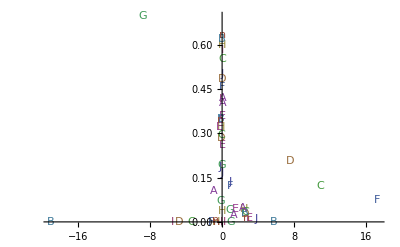

```mathematica
ComparePeaks[CSummaries,CSheets]
```

#### Fitting with fixed peak positions

Recall our literature peak positions:

```mathematica
expositions
```

{-1.8,-0.9,0,1.2,2.3}

```mathematica
AllCModels=FixedPeaksModel[#,{-1.7,-0.9,0,1.2,2.5},0.75]&/@CenteredCData;
```

Sum of squares of residuals: 0.00001825977914836937

Weights | σs
0.0629628 | 0.357438
0.813931 | -0.373651
0.0854521 | -0.560108
0.0190331 | 0.493851
0.018621 | 0.920811

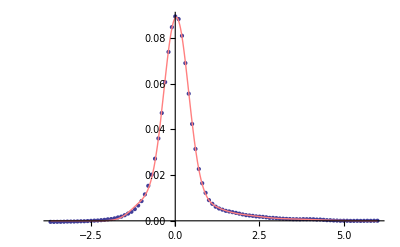

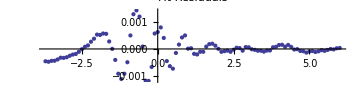

Sum of squares of residuals: 0.000021668715778608385

Weights | σs
0.0100749 | -0.314675
0.211896 | -0.919259
0.651565 | -0.362607
0.0590385 | -0.563076
0.0674259 | 1.20152

Sum of squares of residuals: 0.00005797565937812498

Weights | σs
9.21945×10^-16 | -0.707223
0.000364525 | -0.0840568
0.0493655 | -0.382308
0.841189 | -0.389001
0.109081 | 0.961052

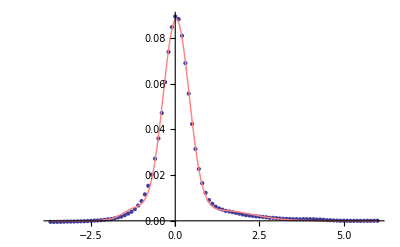

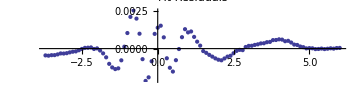

Sum of squares of residuals: 0.000022678471702440266

Weights | σs
0.0872209 | -0.508937
0.0578187 | -0.383193
0.730115 | -0.375016
0.0692662 | -0.510846
0.0555792 | 0.924248

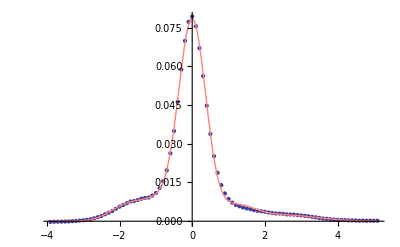

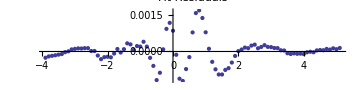

Sum of squares of residuals: 0.00003523830175875379

Weights | σs
2.98796×10^-16 | 0.472747
0.13775 | 0.63587
0.766667 | -0.341689
0.0689169 | 0.49992
0.0266659 | 0.47067

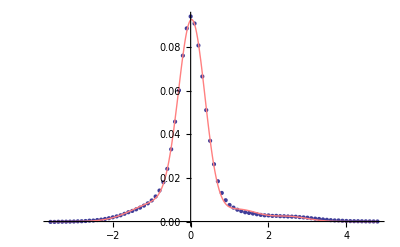

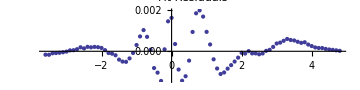

Sum of squares of residuals: 0.000025957674465613434

Weights | σs
0.0273871 | 0.386438
0.0611072 | 0.322162
0.813513 | -0.350145
0.0718494 | 0.509406
0.0261433 | 0.437555

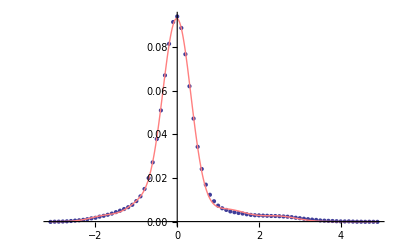

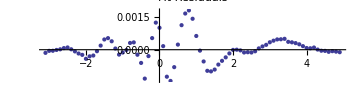

Sum of squares of residuals: 9.311385568527926e-6

Weights | σs
0.10954 | -0.43953
0.762699 | 0.358517
0.0862 | -0.495744
0.0234654 | -0.440912
0.0180957 | 0.757913

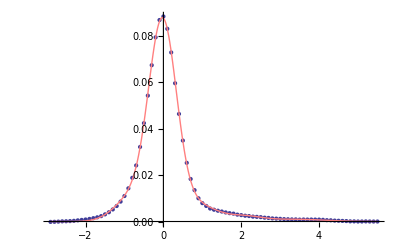

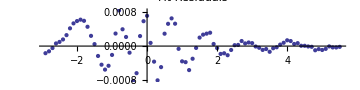

Sum of squares of residuals: 0.00002225837058615573

Weights | σs
0.17698 | 0.559207
0.700136 | 0.343921
0.122701 | 0.922698
4.32685×10^-13 | 0.0139316
0.000182554 | -0.00402957

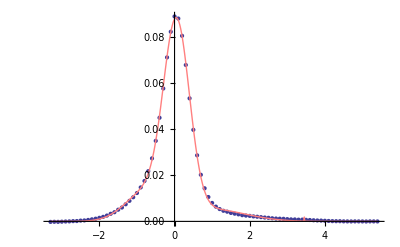

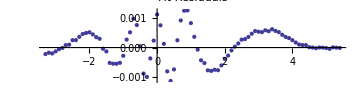

Sum of squares of residuals: 0.000018636399022933526

Weights | σs
0.156404 | -0.76451
0.687267 | -0.345343
0.155512 | -1.1975
7.16768×10^-16 | -0.364443
0.000817243 | -0.0120651

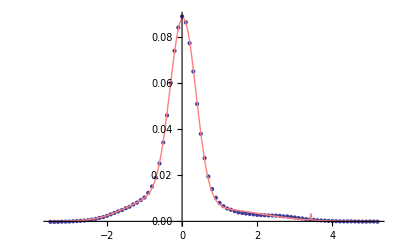

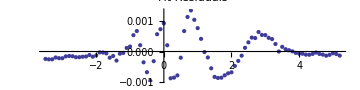

Sum of squares of residuals: 0.000018905491486937838

Weights | σs
0.140837 | 0.736426
0.703601 | 0.337255
0.144696 | -1.04876
4.12118×10^-16 | -0.829087
0.0108668 | 0.640472

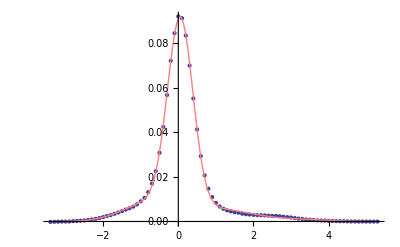

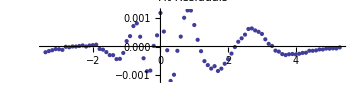

Sum of squares of residuals: 0.000026205626141293305

Weights | σs
2.82847×10^-16 | 0.553166
0.147138 | 0.702735
0.758039 | -0.357525
0.0687439 | 0.507327
0.0260791 | 0.445753

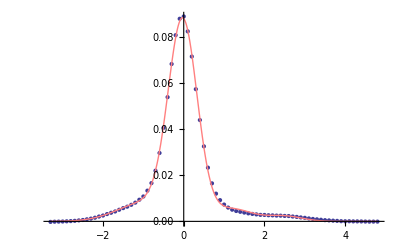

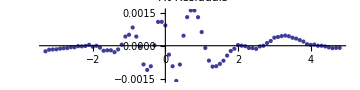

Sum of squares of residuals: 0.000024288182422045448

Weights | σs
0.0313499 | 0.390165
0.067758 | 0.339284
0.803892 | -0.350172
0.0712122 | 0.514697
0.0257875 | 0.443459

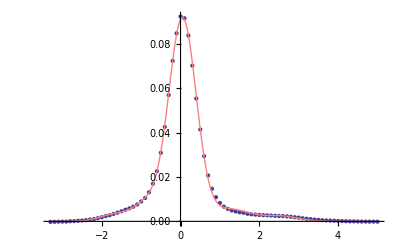

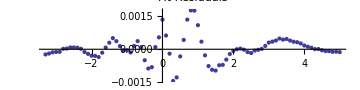

Sum of squares of residuals: 0.00001387703965311649

Weights | σs
2.01188×10^-15 | -0.923383
0.198225 | -0.990708
0.684028 | 0.372856
0.117748 | -1.05436
2.17157×10^-16 | 0.227398

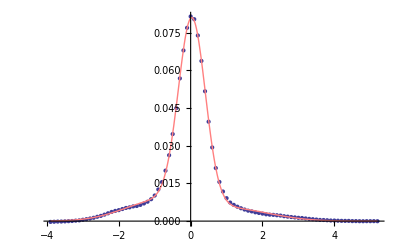

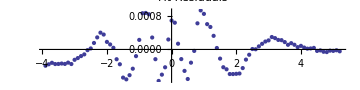

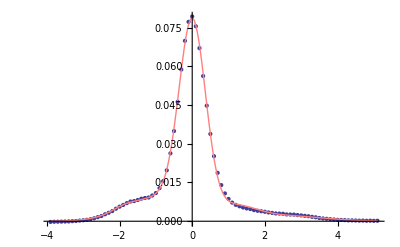

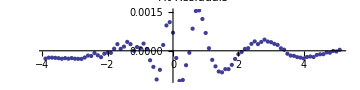

Sum of squares of residuals: 0.00003640875837766229

Weights | σs
0.014819 | 0.376538
0.0992213 | 0.464286
0.751407 | -0.338512
0.106266 | 0.922845
0.0282861 | 2.67439

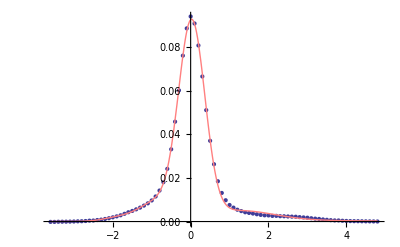

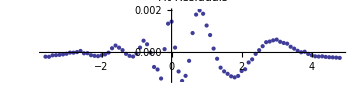

Sum of squares of residuals: 0.000032820228142503276

Weights | σs
0.0142862 | 0.363631
0.0823388 | 0.444443
0.771465 | -0.344315
0.13191 | 1.05085
5.30374×10^-15 | 1.35236

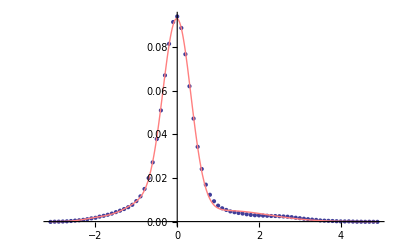

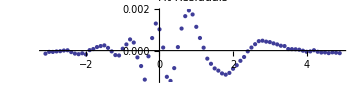

Sum of squares of residuals: 0.00002698240217260203

Weights | σs
0.00816088 | -0.325323
0.0727387 | 0.346618
0.798133 | 0.371777
0.120967 | -0.921627
1.32047×10^-14 | 0.513371

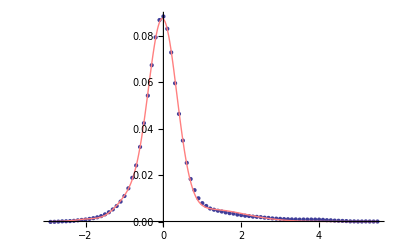

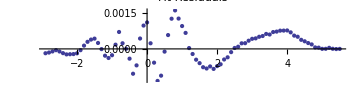

Sum of squares of residuals: 0.00002745234321031896

Weights | σs
0.0141031 | -0.330675
0.128287 | 0.412773
0.761739 | 0.353547
0.0958704 | -0.820576
9.4099×10^-16 | 0.672613

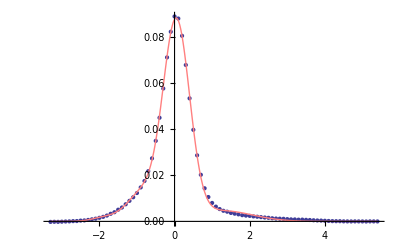

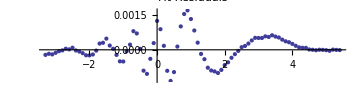

Sum of squares of residuals: 0.000028096257294678256

Weights | σs
1.30666×10^-15 | 0.462712
0.156916 | 0.703908
0.746541 | -0.356502
0.0540651 | 0.489145
0.0424772 | 0.897334

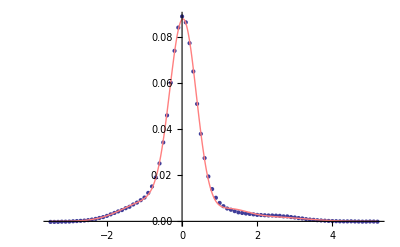

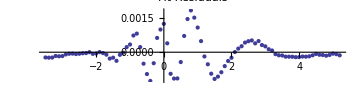

Sum of squares of residuals: 0.00023124268415971997

Weights | σs
0.7713 | 0.361669
0.2287 | -1.98266
4.81679×10^-15 | -3.79191
4.12256×10^-15 | 2.685
2.95973×10^-15 | 0.27117

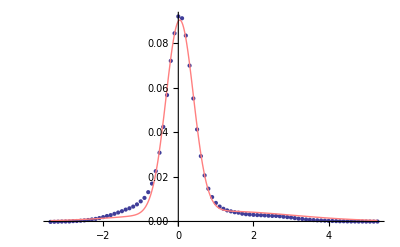

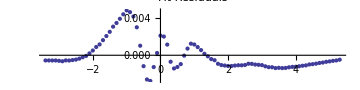

Sum of squares of residuals: 0.00003183860224989418

Weights | σs
5.93487×10^-16 | 0.554582
0.146842 | 0.709414
0.75681 | -0.358491
0.0555345 | 0.502227
0.0408143 | 0.910182

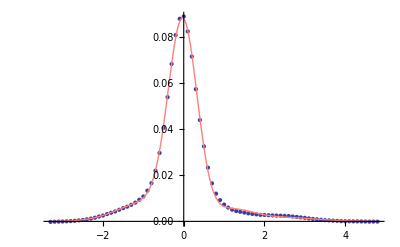

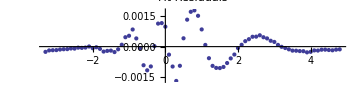

Sum of squares of residuals: 0.000030217516996678472

Weights | σs
0.0153241 | 0.368044
0.0947154 | 0.479105
0.759559 | -0.344343
0.130401 | 1.05469
6.07136×10^-15 | 1.95069

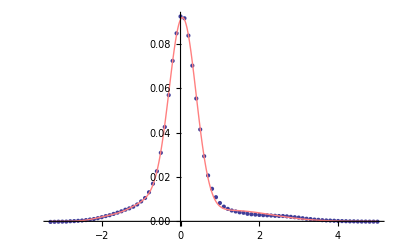

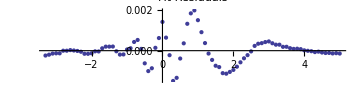

Sum of squares of residuals: 0.000011251225585050373

Weights | σs
0.183188 | 0.893445
0.704585 | 0.373111
0.064032 | 0.53967
0.0480389 | 0.836583
0.000156305 | 0.16984

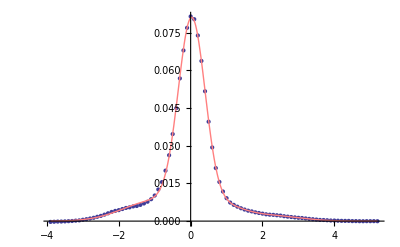

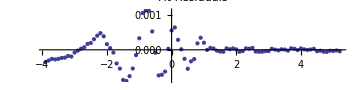

```mathematica
CSummaries=Table[FitSummary[CenteredCData[[x]],AllCModels[[x]],True],{x,1,Length[CenteredCData],1}];
```

### Oxygen Peak

#### Setup

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

#### Fitting with free parameters

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

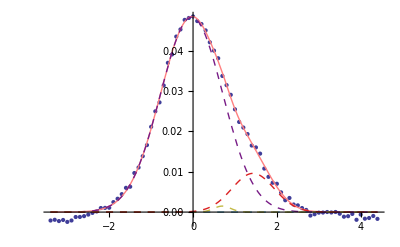

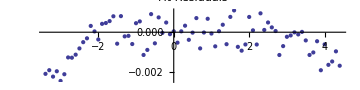

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

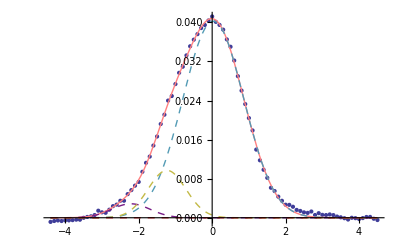

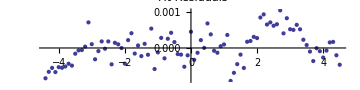

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

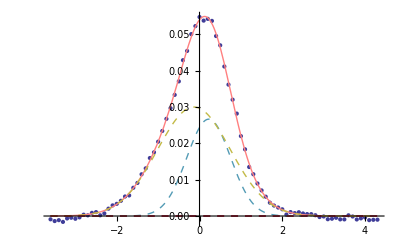

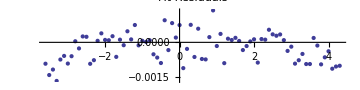

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

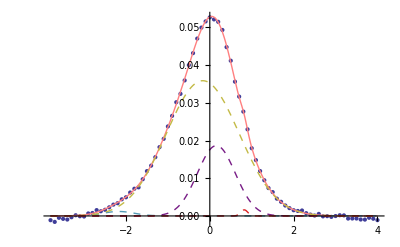

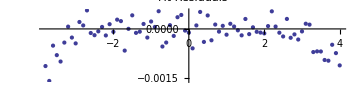

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

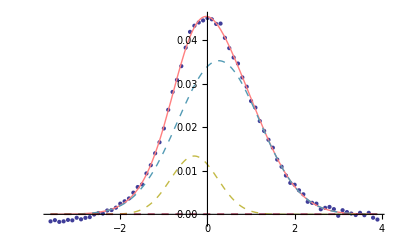

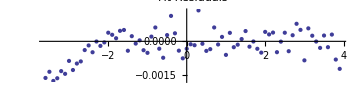

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

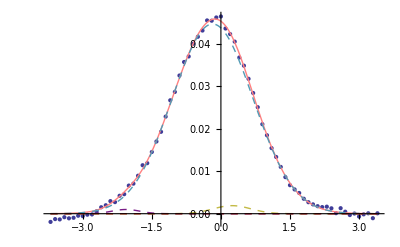

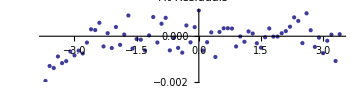

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

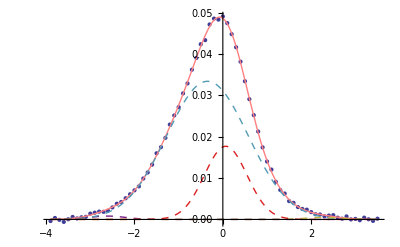

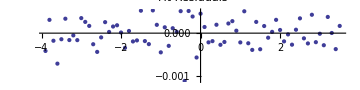

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

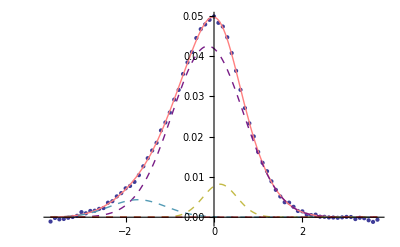

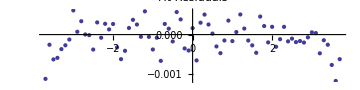

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

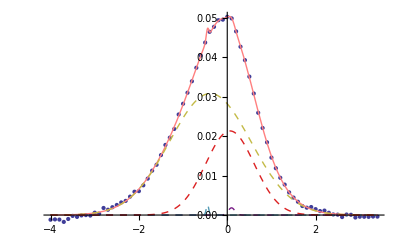

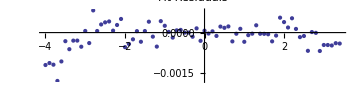

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

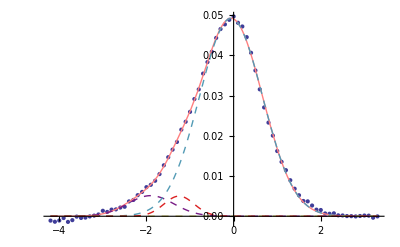

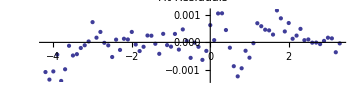

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

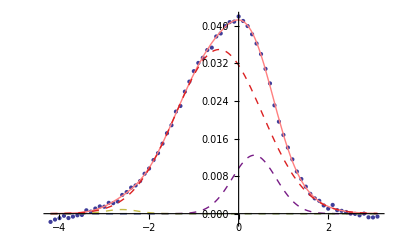

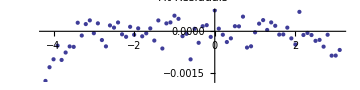

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Visualize location of peaks and weights:

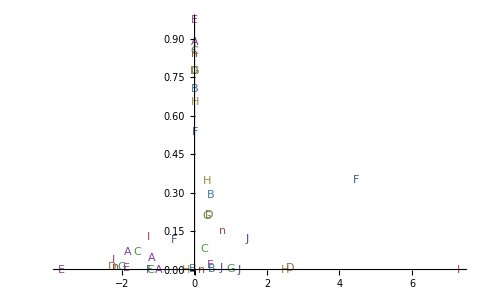

```mathematica
ComparePeaks[OSummaries,OSheets]
```

#### Fitting with fixed peak positions

Fitting works better if the fitting parameters are tweaked a little.

```mathematica
AllOModels=Model[#,4,0.7,0.1]&/@CenteredOData;
```

```mathematica
OSummaries=Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData]}];
```

Weights | Means | σs
0.874396 | 0. | -0.742735
0.118266 | 1.46439 | 0.505756
0.00733787 | 0.730778 | 0.202887
2.38909×10^-15 | 1.22805 | -0.0557857

-Graphics-

-Graphics-

Weights | Means | σs
0.837196 | 0. | 0.828332
0.125163 | -1.26161 | 0.513958
0.0376415 | -2.2437 | -0.524787
1.09389×10^-15 | 7.28843 | 1.13965

-Graphics-

-Graphics-

Weights | Means | σs
0.653603 | 0. | -0.884188
0.346397 | 0.357317 | -0.52724
1.05667×10^-15 | 2.5096 | 0.766575
7.45861×10^-16 | -0.23765 | 0.512961

-Graphics-

-Graphics-

Weights | Means | σs
0.776322 | 0. | -0.873546
0.209321 | 0.324272 | -0.453076
0.0110191 | -2.00676 | -0.375741
0.00333731 | 0.990021 | 0.0838162

-Graphics-

-Graphics-

Weights | Means | σs
0.534729 | 0. | 0.941181
0.348729 | 4.44663 | -0.111634
0.116542 | -0.561733 | -0.540562
7.39575×10^-14 | -1.26733 | -1.66903

-Graphics-

-Graphics-

Weights | Means | σs
0.973399 | 0. | -0.879313
0.0192061 | 0.423804 | 0.40934
0.0073945 | -1.88311 | 0.30123
2.87036×10^-15 | -3.6756 | 2.07797

-Graphics-

-Graphics-

Weights | Means | σs
0.773084 | 0. | -0.923937
0.213826 | 0.413824 | 0.482582
0.00824337 | -2.26355 | -0.406699
0.00484642 | 2.62401 | -0.40358

-Graphics-

-Graphics-

Weights | Means | σs
0.852568 | 0. | -0.806482
0.0785695 | 0.273038 | 0.385294
0.0688621 | -1.58587 | 0.637021
2.53352×10^-11 | -1.22528 | 1.09366

-Graphics-

-Graphics-

Weights | Means | σs
0.702948 | 0. | -0.919186
0.291838 | 0.446328 | 0.551286
0.00336372 | 0.48207 | -0.0744654
0.00184975 | -0.0628031 | 0.0283305

-Graphics-

-Graphics-

Weights | Means | σs
0.888669 | 0. | -0.722229
0.0680254 | -1.84434 | 0.530839
0.043306 | -1.19196 | 0.345794
1.55702×10^-15 | -0.987686 | -1.7759

-Graphics-

-Graphics-

Weights | Means | σs
0.841105 | 0. | 0.969829
0.151044 | 0.784281 | -0.489246
0.0078509 | -2.1727 | -0.36118
4.66842×10^-14 | 0.20277 | -0.484569

-Graphics-

-Graphics-

Visualize location of peaks and weights:

```mathematica
ComparePeaks[OSummaries,OSheets]
```

-Graphics-